Министерство образования и науки Российской Федерации 
Федеральное государственное бюджетное образовательное учреждение высшего образования «Тульский государственный университет»


Кафедра «Информационной безопасности»






ИССЛЕДОВАНИЕ ГЕНЕТИЧЕСКИХ АЛГОРИТМОВ

отчет по 
лабораторной работе №4

по курсу
 
ТЕОРИЯ ИНФОРМАЦИОННЫХ СИСТЕМ 


ВАРИАНТ 14





Выполнил:               студент группы  220441         _________    Шипулин П.С.
           				(подпись)
 Проверил:	              профессор. каф. ИБ               _________   Богатырев М. Ю.
           				(подпись)










Тула, 2017 г.

## Цель и задача работы

Целью работы является приобретение практических навыков работы с эволюционными методами оптимизации на примере генетического алгоритма.

## Задание на работу

1) Получить тестовую функцию
2) Модифицировать программу GA_Mma_v9.nb для заданной
тестовой функции.
3) Выполнить решение задачи поиска экстремума тестовой функции генетическим алгоритмом и при помощи соответствующей функции системы Mathematica. Сравнить полученные решения.
4) Исследовать влияние параметров генетического алгоритма на результаты поиска экстремума тестовой функции:
- размера популяции решений;
- величины мутации;
- длины строки хромосомы.
5) Меняя величины параметров в п. 4.4, сравнивать решения, получаемые при помощи генетического алгоритма и функций системы Mathematica согласно п. 

Тестовая функция:f(x)=-∑_(i=1)^m [(x-a_i)(x-a_i)^T+c_i]^-1, где m=5,7 и 10, 0≤ x_j≤ 10, а j=2.

Таблица 1 - Функции Шекеля f_21, f_22, f_23
-Graphics-

## Ход работы

1) Для решения поставленной задачи мною была доработана программа по нахождению экстремумов путем подстановки в неё своей функции и добавлением дополнительных данных, необходимых для её вычисления. Текст программы представлен ниже:

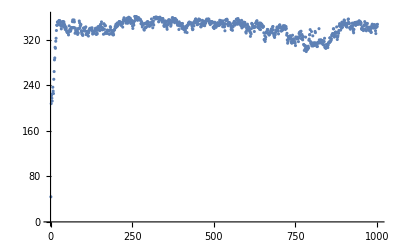

-Graphics3D-

-Graphics3D-

```mathematica
(* Задание параметров генетического алгоритма *)
dim=2;(* Размерность исследуемой функции *)
(*В программе применяется трехмерная визуализация функций*)
(*В качестве двух переменных - аргументов можно выбирать любые две переменные многомерной функции*)
one=1;(* Первая переменная - аргумент*)
two=2;(* Вторая переменная *)
(* Если разменрность функции больше двух, то для визуализации остальные переменные должны быть константами, наприме:  var[3]=5,etc.*)
m:=5;
c={0.1,0.2,0.2,0.4,0.4,0.6,0.3,0.7,0.5,0.5};
a={{4,4,4,4},{1,1,1,1},{8,8,8,8},{6,6,6,6},{3,7,3,7},{2,9,2,9},{5,5,3,3},{8,1,8,1},{6,2,6,2},{7,3.6,7,3.6}};


cnt=1; (* Счетчик*)
stringLength = 60;   (* Длина хромосомы *)
mutationRate = 0.002;   (* Вероятность мутации *)
popSize = 64;   (* Размер популяции (четное число)*)
part = 0.001;       (*точность вычисления значений функции пригодности*)                                                
compareSums = 3;    (*число подряд идущих сравниваемых значений функции пригодности*)                                                
limitPop = 1000;     (*максимальное число популяций*)     
Array[popFl,dim];
Array[popStr,dim];
Array[popS,dim];
Array[historyOfP,dim];
Array[per,dim];
Array[var,dim];
	Array[var,dim];

Off[General::spell];   (* Отключение предупреждений *)

(* Перевод значений с плавающей точкой в бинарные строки*)
Clear[floatToBinary];
floatToBinary[x_] := Module[{temp},
	temp = RealDigits[ x, 2 ];
	Take[ Join[ 
		Table[0, {-temp[[2]]}], temp[[1]], Table[0, {stringLength}] ],
		stringLength ]
] /; x<5                  (* x<25 для устаноновки диапазона изменения случайной величины; зависит от интервала поиска *)

(* Перевод значений с плавающей точкой в бинарные строки*)
Clear[binaryStringToFloat];

binaryStringToFloat[string_]:=10*(0.5-
	N[Sum[ string[[i]]*2^(-i), {i, Length[string]} ]])+5     (* Здесь 10 задает ширину интервала изменения переменной *)

(* Нормализация функции пригодности популяции*)
Clear[renormalizeFitness];
renormalizeFitness[fitness_List] := Module[{minF,maxF,a,b},
	minF = Min[fitness];
	maxF = Max[fitness];
	a = 0.5*maxF/(maxF+minF);
	b = (1-a)*maxF;
	Map[ a# + b &, fitness ]
]

(* Создание начальной популяции *)
While[cnt<dim+1,popFl[cnt] = Table[ Random[Real,{0,1}], {popSize} ];cnt++];
		cnt=1;                                             
While[cnt<dim+1,popStr[cnt]=Map[floatToBinary,popFl[cnt]];cnt++];
cnt=1;
While[cnt<dim+1,popS[cnt]=popStr[cnt];cnt++];
cnt=1;
While[cnt<dim,popStrings=MapThread[Join,{popS[cnt],popS[cnt+1]}];popS[cnt+1]=popStrings;cnt++];
cnt=1;
(* Определение функции пригодности  нескольких аргументов*)
Clear[fitnessFunction];
fitnessFunction[x1_,x2_]:=
Sum[((x1-a[[i,1]])^2+(x2-a[[i,2]])^2+c[[i]])^-1,{i,m}]
(* Функция ркомбинации *)	
Clear[doSingleCrossover];
doSingleCrossover[ {string1_, string2_} ] := Module[{stle,cut,temp1,temp2},
	stle = Length[string1];
	cut = Random[Integer, {1,stle-1}];
	temp1 = Join[ Take[string1, cut],
		Drop[string2, cut] ];
	temp2 = Join[ Take[string2, cut],
		Drop[string1, cut] ];
	{temp1, temp2} ]

(* функция мутации с вероятностью mutationRate *)
Clear[doMutation];
doMutation[string_] := Module[{tempstring,i},
	tempstring = string;
	Do[ If[ Random[] < mutationRate,
		tempstring[[i]] = 1 - tempstring[[i]] ],
		{i,stringLength} ];
	tempstring
]

Clear[doCumSumOfFitness];
doCumSumOfFitness := Module[{temp},
	temp = 0.0;
	Table[ temp += popFitness[[i]], {i, popSize} ]
]

Clear[doSingleSelection];
doSingleSelection := Module[{rfitness,ind},
	rfitness = Random[Real, {0, cumFitness[[popSize]]}];
	ind = 1;
	While[ rfitness > cumFitness[[ind]], ind++ ];
	ind--
]

Clear[selectPair];
selectPair := Module[{ind1,ind2},
	ind1 = doSingleSelection;
	While[ (ind2 = doSingleSelection) == ind1, ];
	{ind1, ind2}
]

(* Функция инициализации, использующая функцию пригодности*)
Clear[doInitialize];
doInitialize := Module[{i},
	While[cnt<dim+1,per[cnt]=Table[binaryStringToFloat[popStr[cnt][[i]]],{i,popSize}];cnt++];
		cnt=1;
		popFitness = Apply[fitnessFunction,Array[per,dim]];
	cumFitness = doCumSumOfFitness;
	listOfCumFitness = {cumFitness[[popSize]]};
	(* Эволюция популяций отслеживается для каждой переменной *)
		historyOfPop = { popStrings };
		While[cnt<dim+1,historyOfP[cnt] = { popStr[cnt] };cnt++];
		cnt=1;
	
]

Clear[updateGenerationSync];



updateGenerationSync := Module[{parentsid,children,ip},
	parentsid = {};
	Do[	AppendTo[ parentsid, selectPair ], {popSize/2} ];
	children = {};
	Do[ AppendTo[ children, 
			doSingleCrossover[ {popStrings[[parentsid[[ip,1]]]], 
			popStrings[[parentsid[[ip,2]]]]} ] ],
		{ip, popSize/2} ];
	popStrings = Flatten[ children, 1];
	popStrings = Map[ doMutation, popStrings ]; 


takesl[list_]:=Take[list,stringLength];
dropsl[list_]:=Drop[list,stringLength];
popSt=popStrings;
While[cnt<dim+1,popStr[cnt]=Map[takesl,popSt];popSt=Map[dropsl,popSt];cnt++];
cnt=1;

While[cnt<dim+1,per[cnt]=Map[binaryStringToFloat,popStr[cnt]];cnt++];
		cnt=1;
popFitness = Apply[fitnessFunction,Array[per,dim]];
popFitness = renormalizeFitness[ popFitness ];
cumFitness = doCumSumOfFitness;	
];


doInitialize;
test = True;
countPop = 1;
While[	test,
	updateGenerationSync;
	AppendTo[ historyOfPop, popStrings ];
	While[cnt<dim+1,	AppendTo[ historyOfP[cnt], popStr[cnt] ];cnt++];
	cnt=1;
	AppendTo[ listOfCumFitness, cumFitness[[popSize]] ]; 
	countPop++;
	If[ countPop>compareSums, 
	testSum=0;
	Do[ If[ Abs[(listOfCumFitness[[countPop-compS+1]] - listOfCumFitness[[countPop-compS]])] < part×listOfCumFitness[[countPop-compS+1]], testSum++; ];,
	{compS,compareSums}];
	If[(testSum==compareSums)||(countPop>limitPop), test=False;]
	  ];
	];
(*Вывод графика изменения пригодности*)
ListPlot[ listOfCumFitness,PlotRange->All ]

fitFun[y1_,y2_]=Evaluate[Apply[fitnessFunction,Array[var,dim]]];
(*Вывод графика исследуемой функции*)
fitnessplot = Plot3D[fitnessFunction[var[one],var[two]], {var[one], 0, 10},{var[two],0,10},PlotRange->All, 
	Axes->True,PlotPoints->18,
	DisplayFunction->Identity];

graphicsSingleGeneration[igen_] := Module[{graphelement,x1,x2},
	graphelement = {};
	Do[	x1 = binaryStringToFloat[ historyOfP[one][[igen,i]] ];
			x2 = binaryStringToFloat[ historyOfP[two][[igen,i]] ];
					var[one]=x1;var[two]=x2;
		AppendTo[ graphelement, 
			Graphics3D[ {PointSize[0.02],RGBColor[1,0,0],Point[{var[one],var[two],fitnessFunction[var[one],var[two]]} ]}] ],
		{i, popSize} ];
	graphelement
]
(*Показ начальной популяции на графике функции*)
Show[  fitnessplot,graphicsSingleGeneration[1], 
	PlotRange->All,ViewPoint->{-1.330,-1.010,2.000},
		DisplayFunction->$DisplayFunction]
(*Показ конечной популяции на графике функции*)
Show[ fitnessplot, graphicsSingleGeneration[Length[ historyOfPop ]], 
		PlotRange->All,ViewPoint->{-1.330,-1.010,2.000},
		DisplayFunction->$DisplayFunction ]
```

Далее представлены результаты выполнения программы:

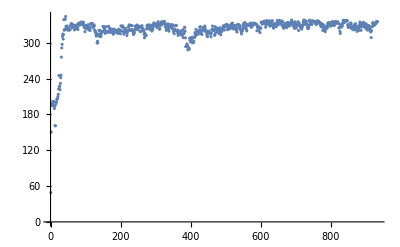

Рисунок 1 - График изменения пригодности

Рисунок 2 - График, показывающий начальную популяцию

Далее я буду изменять параметры размера популяции. Результаты приведены для популяций размером 16, 32, 64 и 128

```mathematica
-Graphics3D- -Graphics3D--Graphics3D--Graphics3D-
```

В зависимости от размера популяции изменялись и результаты нахождения экстремумов. При большей популяции результат выходил точнее.
Далее будут изменяться величина мутации при размере популяции, равном 64. 0,002; 0,004; 0,008;0,016; 0,128

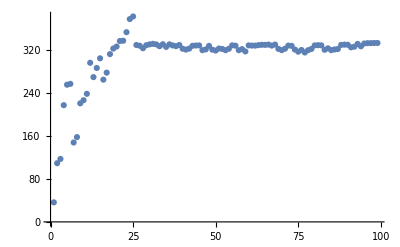
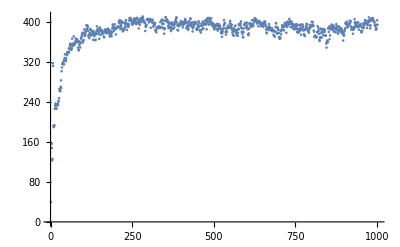
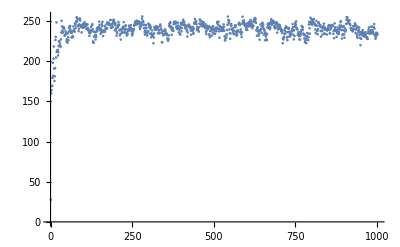
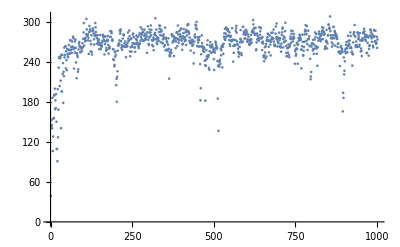
```mathematica
-Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D-
		-Graphics--Graphics--Graphics--Graphics--Graphics-
```

(*Вывод должен быть здесь*)

Далее я буду изменять длину хромосомы. Величина популяции - 64; Вероятность мутации - 0,002; Длинна хромосомы - 5, 10, 20, 60
Результаты приведены далее.

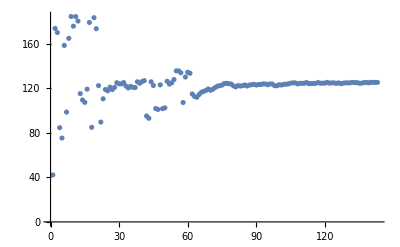
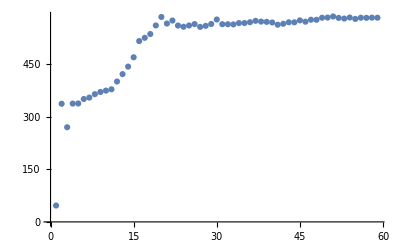
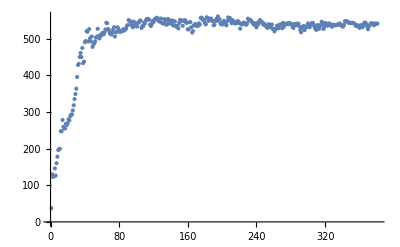
```mathematica
-Graphics3D--Graphics3D--Graphics3D--Graphics3D-
-Graphics--Graphics--Graphics--Graphics-
```

Код Грея????????